## NF theory for sequential dynamics

```mathematica
SetDirectory["/home/shubham/Dropbox/Shubham/Turing_submission/Code"];
```

```mathematica
t1data=Import["Marcon_data_bsw/t1.csv"];
t2data=Import["Marcon_data_bsw/t2.csv"];
t3data=Import["Marcon_data_bsw/t3.csv"];
```

```mathematica
t1data=Drop[t1data,1];
t2data=Drop[t2data,1];
t3data=Drop[t3data,1];
```

### Data without mean

```mathematica
t1wm=Transpose[{t1data[[2;;-1]][[All, 1]], t1data[[2;;-1]][[All, 2]]-Mean[t1data[[2;;-1]][[All, 2]]]}];
t2wm=Transpose[{t2data[[2;;-1]][[All, 1]], t2data[[2;;-1]][[All, 2]]-Mean[t2data[[2;;-1]][[All, 2]]]}];
t3wm=Transpose[{t3data[[2;;-1]][[All, 1]], t3data[[2;;-1]][[All, 2]]-Mean[t3data[[2;;-1]][[All, 2]]]}];
```

```mathematica
d1=LowpassFilter[t1wm[[1;;All,2]],1];
d1x=Table[{t1wm[[i,1]],d1[[i]]},{i,1,Dimensions[d1][[1]]}];
```

```mathematica
d2=LowpassFilter[t2wm[[1;;All,2]],1];
d2x=Table[{t2wm[[i,1]],d2[[i]]},{i,1,Dimensions[d2][[1]]}];
```

```mathematica
d3=LowpassFilter[t3wm[[1;;All,2]],1];
d3x=Table[{t3wm[[i,1]],d3[[i]]},{i,1,Dimensions[d3][[1]]}];
```

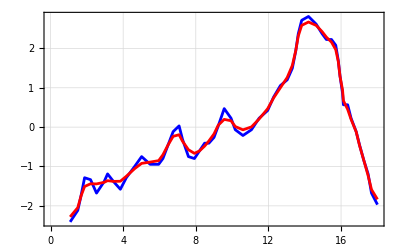

```mathematica
ListLinePlot[{t1wm,d1x},PlotStyle->{Blue,Red},Frame->True,GridLines->Automatic]
```

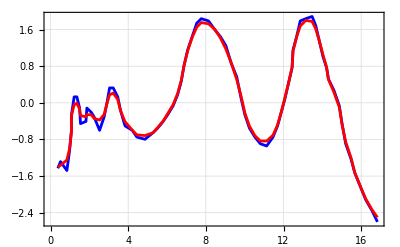

```mathematica
ListLinePlot[{t2wm,d2x},PlotStyle->{Blue,Red},Frame->True,GridLines->Automatic]
```

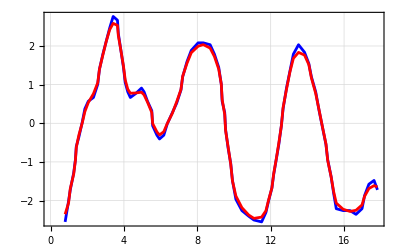

```mathematica
ListLinePlot[{t3wm,d3x},PlotStyle->{Blue,Red},Frame->True,GridLines->Automatic]
```

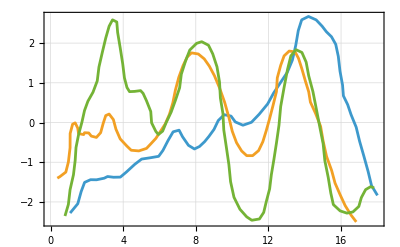

```mathematica
ListLinePlot[{d1x,d2x,d3x},Frame->True,GridLines->Automatic]
```

```mathematica
eval=Thread[{α,β,γ,δ,da,db}->{19.5,-42,25,-50,3,15}];
```

```mathematica
{x0,xL}={0,6Pi-1};
boxleft[x_]:=UnitStep[x-2Pi]
boxright[x_]:=UnitStep[-x+4Pi]
box[x_]:=UnitStep[x-4Pi]+UnitStep[-x+2Pi]
```

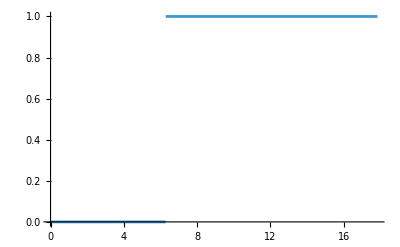

```mathematica
Plot[boxleft[x],{x,x0,xL}]
```

```mathematica
ev=NDEigensystem[{α(1-0.3box[x])a[x]+β b[x]+da a''[x],γ a[x]+δ b[x]+db b''[x]}/.eval,{a[x],b[x]},{x,x0,xL},5];
```

```mathematica
ev[[1]]
```

{-0.0118556,0.0351492,-1.66036,-1.70281,-4.20101}

```mathematica
ev[[2,2]][[2]]
```

InterpolatingFunction[…][x]

```mathematica
evbox=InterpolatingFunction[…];
```

```mathematica
shiftev[x_?NumericQ,delta_]:=Module[{xShifted},xShifted=x-delta;
Piecewise[{{-evbox[xShifted],0<=xShifted<=xL}},0]]
```

```mathematica
evleft=NDEigensystem[{α(1-0.3boxleft[x])a[x]+β b[x]+da a''[x],γ a[x]+δ b[x]+db b''[x]}/.eval,{a[x],b[x]},{x,x0,xL},5];
```

```mathematica
evleft[[2,2]][[2]]
```

InterpolatingFunction[…][x]

```mathematica
evboxleft=InterpolatingFunction[…];
```

```mathematica
shiftevleft[x_?NumericQ,delta_]:=Module[{xShifted},xShifted=x-delta;
Piecewise[{{-evboxleft[xShifted],0<=xShifted<=xL}},0]]
```

```mathematica
evright=NDEigensystem[{α(1-0.3boxright[x])a[x]+β b[x]+da a''[x],γ a[x]+δ b[x]+db b''[x]}/.eval,{a[x],b[x]},{x,x0,xL},5];
```

```mathematica
evright[[2,2]][[2]]
```

InterpolatingFunction[…][x]

```mathematica
evboxright=InterpolatingFunction[…];
```

```mathematica
shiftevright[x_?NumericQ,delta_]:=Module[{xShifted},xShifted=x-delta;
Piecewise[{{evboxright[xShifted],0<=xShifted<=xL}},0]]
```

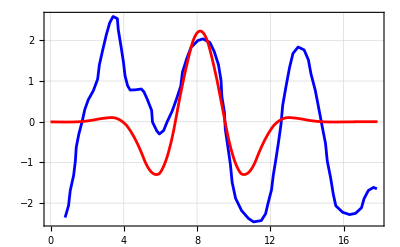

```mathematica
Show[{ListLinePlot[d3x,Frame->True,GridLines->Automatic,PlotStyle->Blue],Plot[10shiftev[x,-1.2],{x,x0,xL},PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Red](*Plot[10shiftevright[x,-1.5],{x,x0,xL},PlotRange->All],Plot[10shiftevleft[x,0.8],{x,x0,xL},PlotRange->All]*)},PlotRange->All]
```

#### Fit with experimental data

```mathematica
{s1,s2,s3}={-1.35,-1.2,0.6}
```

{-1.35,-1.2,0.6}

```mathematica
nlm1 = {a, b,c} /. NonlinearModelFit[d1x, a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3], {a, b,c}, x]["BestFitParameters"]
```

{2.18206,-0.481815,-0.748658}

```mathematica
nlm2 = {a, b,c} /. NonlinearModelFit[d2x, a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3], {a, b,c}, x]["BestFitParameters"]
```

{6.84638,6.76359,0.172595}

```mathematica
nlm3 = {a, b,c} /. NonlinearModelFit[d3x, a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3], {a, b,c}, x]["BestFitParameters"]
```

{9.75405,7.04033,7.1453}

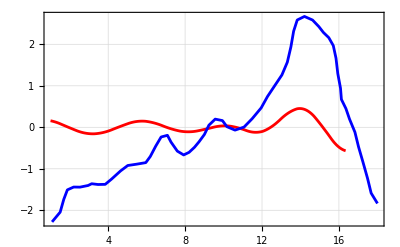

```mathematica
Show[Plot[a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->nlm1],{x,x0+1,xL-1.5},PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Red],ListLinePlot[d1x,PlotStyle->Blue],PlotRange->All]
```

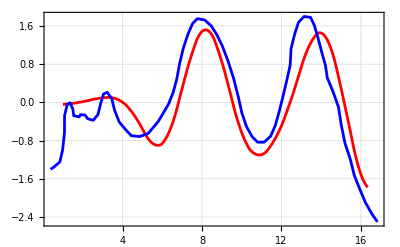

```mathematica
Show[Plot[a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->nlm2],{x,x0+1,xL-1.5},PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Red],ListLinePlot[d2x,PlotStyle->Blue],PlotRange->All]
```

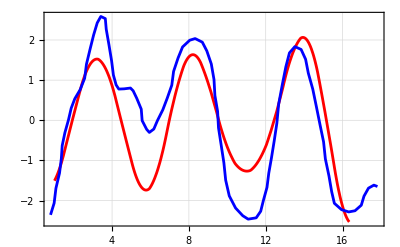

```mathematica
Show[Plot[a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->nlm3],{x,x0+1,xL-1.5},PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Red],ListLinePlot[d3x,PlotStyle->Blue],PlotRange->All]
```

#### Adding coefficients manually

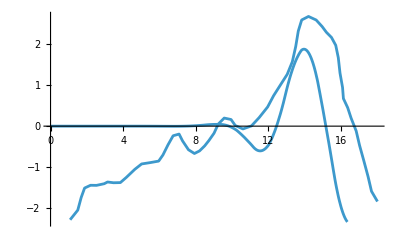

```mathematica
plt1=Show[Plot[a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->{9,0.0,0.0}],{x,x0,xL-1.5},PlotRange->All],ListLinePlot[d1x],PlotRange->All]
```

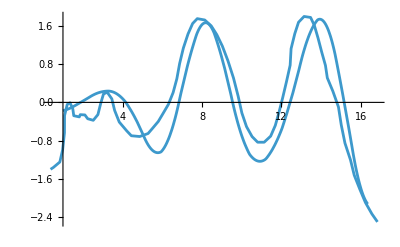

```mathematica
plt2=Show[Plot[a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->{8.2,7.4,0.8}],{x,x0+1,xL-1.5},PlotRange->All],ListLinePlot[d2x],PlotRange->All]
```

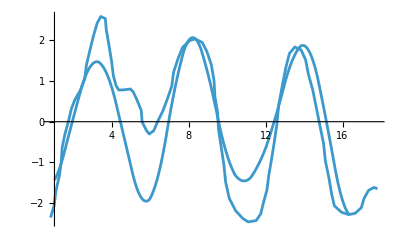

```mathematica
plt3=Show[Plot[a shiftevright[x,s1] + b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->{8.8,9,6.8}],{x,x0+1,xL-1.5}],ListLinePlot[d3x],PlotRange->All]
```

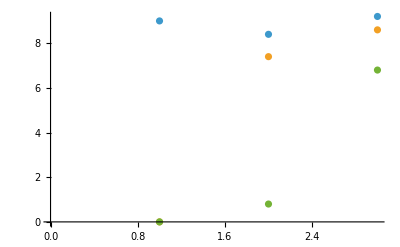

```mathematica
ListPlot[Transpose[{{9,0.0,0},{8.4,7.4,0.8},{9.2,8.6,6.8}}]]
```

#### Ignoring the first domain, and starting with t1data remove the mean

```mathematica
t1datadrop=Drop[t1data,26];
t1datadrop=Drop[t1datadrop,-7];
```

```mathematica
t1wmdrop=Transpose[{t1datadrop[[2;;-1]][[All, 1]], t1datadrop[[2;;-1]][[All, 2]]-Mean[t1datadrop[[2;;-1]][[All, 2]]]}];
```

```mathematica
d1drop=LowpassFilter[t1wmdrop[[All,2]],1];
```

```mathematica
d1xdrop=Table[{t1wmdrop[[i,1]],d1drop[[i]]},{i,Dimensions[d1drop][[1]]}];
```

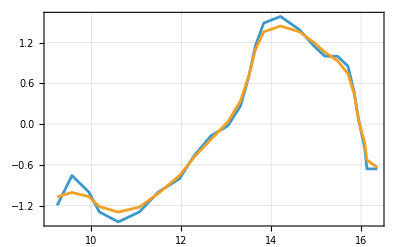

```mathematica
ListLinePlot[{t1wmdrop,d1xdrop},Frame->True,GridLines->Automatic]
```

```mathematica
nlm1drop={a, b} /. NonlinearModelFit[d1xdrop, a shiftevright[x,s1]+ b shiftev[x,s2], {a, b}, x]["BestFitParameters"]
```

{2.4959,8.83544}

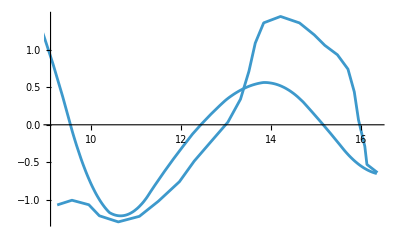

```mathematica
Show[ListLinePlot[d1xdrop],Plot[a shiftevright[x,s1]+ b shiftev[x,s2]/.Thread[{a,b}->nlm1drop],{x,2Pi,xL-1.5}]]
```

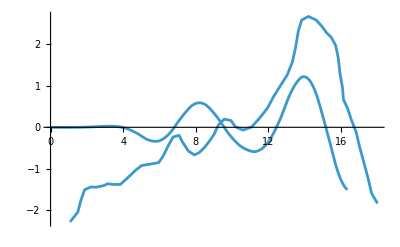

```mathematica
Show[ListLinePlot[d1x],Plot[a shiftevright[x,s1]+ b shiftev[x,s2]/.Thread[{a,b}->{5.8,2.6}],{x,0,xL-1.5}],PlotRange->All]
```

```mathematica
m=Mean[t1datadrop[[2;;-1]][[All, 2]]];
```

```mathematica
t1wm2=Transpose[{t1data[[2;;-1]][[All, 1]], t1data[[2;;-1]][[All, 2]]-m}];
```

```mathematica
d12=LowpassFilter[t1wm2[[1;;All,2]],1];
d1x2=Table[{t1wm2[[i,1]],d12[[i]]},{i,1,Dimensions[d12][[1]]}];
```

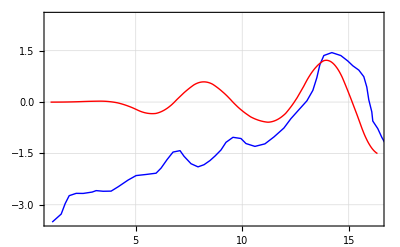

```mathematica
plt1=Show[ListLinePlot[d1x2,PlotStyle->{Thick,Blue},FrameTicks->{Automatic,{Table[{x,ToString[x]},{x,0,15,5}],None}}],Plot[a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->{5.8,2.6,0}],{x,x0+1,xL-1.5},PlotStyle->{Thick,Red}],PlotRange->{{x0+1,xL-1.5},{-3.5,2.5}},Frame->True,GridLines->Automatic]
```

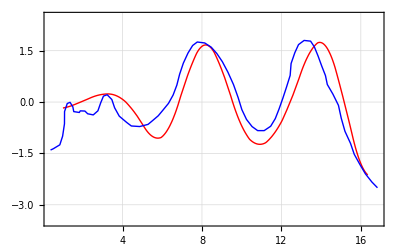

```mathematica
plt2=Show[Plot[a shiftevright[x,s1]+ b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->{8.2,7.4,0.8}],{x,x0+1,xL-1.5},PlotStyle->{Thick,Red}],ListLinePlot[d2x,PlotStyle->{Thick,Blue}],PlotRange->{-3.5,2.5},Frame->True,GridLines->Automatic]
```

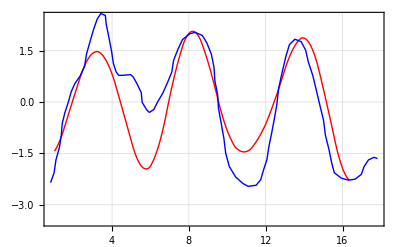

```mathematica
plt3=Show[Plot[a shiftevright[x,s1] + b shiftev[x,s2]+c shiftevleft[x,s3]/.Thread[{a,b,c}->{8.8,9,6.8}],{x,x0+1,xL-1.5},PlotStyle->{Thick,Red}],ListLinePlot[d3x,PlotStyle->{Thick,Blue}],PlotRange->{-3.5,2.5},Frame->True,GridLines->Automatic]
```

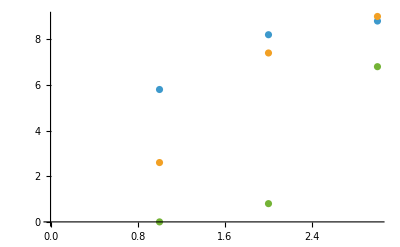

```mathematica
rdyn=ListPlot[Transpose[{{5.8,2.6,0},{8.2,7.4,0.8},{8.8,9,6.8}}]]
```

#### Fitting the r dynamics

```mathematica
data={{2,5.8,2.6,0},{3,8.2,7.4,0.8},{4,8.8,9,6.8}};
```

```mathematica
p1=Table[{data[[i,1]],data[[i,2]]},{i,3}];
p2=Table[{data[[i,1]],data[[i,3]]},{i,3}];
p3=Table[{data[[i,1]],data[[i,4]]},{i,3}];
```

```mathematica
p3={{2,0},{3,0.8},{4,6.8},{5,9}}
```

{{2,0},{3,0.8},{4,6.8},{5,9}}

```mathematica
rsol=DSolve[{r'[t]==a1 r[t]-a2 r[t]^3,r[0]==r0},r[t],t,Assumptions->{r0>0,p1>0,p2>0}]//Quiet//FullSimplify;
```

```mathematica
functofit=r[t]/.rsol[[1,1]]
```

(√a1 ⅇ^(a1 t) r0)/(√(a1-a2 r0^2) √(1+(a2 ⅇ^(2 a1 t) r0^2)/(a1-a2 r0^2)))

```mathematica
nlmf1 = NonlinearModelFit[p1, functofit, {{a1,1.7}, {a2,0.02}, {r0, 0.21}}, t]
```

FittedModel[…]

```mathematica
nlmf3["BestFitParameters"]
```

nlmf3[BestFitParameters]

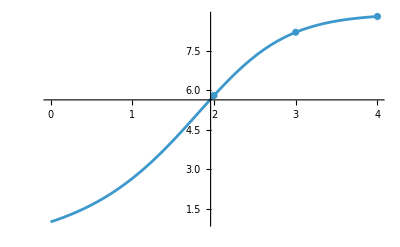

```mathematica
Show[ListPlot[p1],Plot[Evaluate[functofit/.nlmf1["BestFitParameters"]],{t,0,4}],PlotRange->All]
```

```mathematica
nlmf2 = NonlinearModelFit[p2, functofit, {{a1,1.7}, {a2,0.02}, {r0, 0.21}}, t]
```

FittedModel[…]

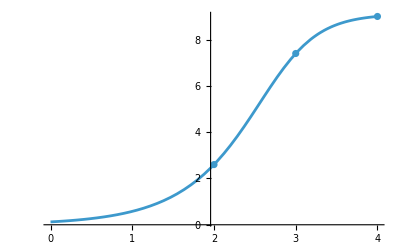

```mathematica
Show[ListPlot[p2],Plot[Evaluate[functofit/.nlmf2["BestFitParameters"]],{t,0,4}],PlotRange->All]
```

```mathematica
nlmf3 = NonlinearModelFit[p3, functofit, {{a1,3}, {a2,0.01}, {r0, 0.004}}, t]
```

FittedModel[…]

```mathematica
plt1=Show[ListPlot[p1],Plot[Evaluate[functofit/.nlmf1["BestFitParameters"]],{t,1,4}],PlotRange->All,Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}];
```

```mathematica
plt2=Show[ListPlot[p2],Plot[Evaluate[functofit/.nlmf2["BestFitParameters"]],{t,1,4}],PlotRange->All,Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}];
```

```mathematica
plt3=Show[ListPlot[p3],Plot[Evaluate[functofit/.nlmf3["BestFitParameters"]],{t,1,4}],PlotRange->All,Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}];
```

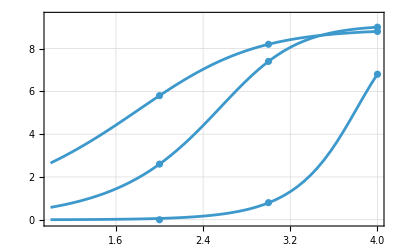

```mathematica
sox9fit=Show[plt1,plt2,plt3,PlotRange->{{1,4},{-0.1,9.5}}]
```

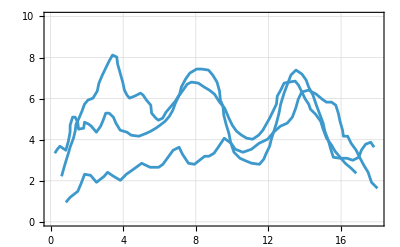

```mathematica
sox9data=Show[ListLinePlot[t1data,PlotRange->{0,10}],ListLinePlot[t2data,PlotRange->{0,10}],ListLinePlot[t3data,PlotRange->{0,10}],Frame->True,GridLines->Automatic]
```

#### Checking the mean of two halves

```mathematica
{t1data[[29,1]],t2data[[43,1]],t3data[[50,1]]}
```

{9.56542,9.30782,9.54168}

```mathematica
{Mean[t1data[[1;;28,2]]],Mean[t1data[[29;;All,2]]]}
```

{2.58537,4.41006}

```mathematica
{Mean[t2data[[1;;42,2]]],Mean[t2data[[43;;All,2]]]}
```

{4.96167,4.92539}

```mathematica
{Mean[t3data[[1;;49,2]]],Mean[t3data[[50;;All,2]]]}
```

{5.99751,4.49512}